```mathematica
SetDirectory[NotebookDirectory[]];
```

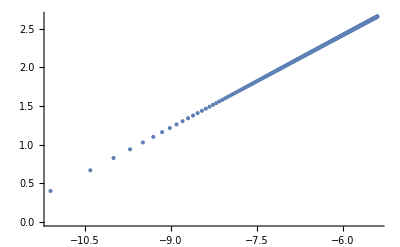

```mathematica
fpi=Flatten[Import["./fpi.dat"]];
T=Flatten[Import["./TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
Tdata=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
a1=Table[FindFit[Tdata[[i-1;;i+1]],a+b x,{a,b},x][[1]][[2]],{i,2,Length[T]-2}];
b1=Table[FindFit[Tdata[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}];
Show[ListPlot[{Tdata},PlotRange->All]]
```

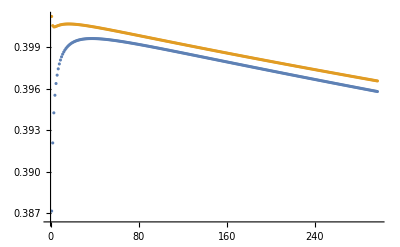

```mathematica
ListPlot[{b1,b1300},PlotRange->All]
```